2.2062×10^8 (1/r^2)^(1/4)+2.82188×10^7 (1/(r-rp)^2)^(1/4)

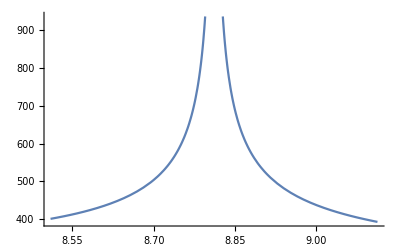

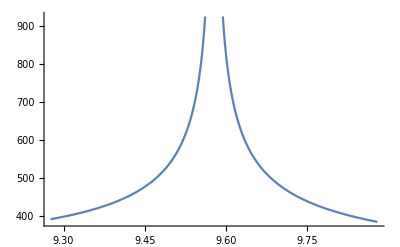

21.8866

15.9549

14.4465

9.21309

```mathematica
σ=5.67*10^-8;
r0=0;
r1=.8811*10^12;
r2=3.015*10^10;
L0=1.688*10^27;
L1=4.518*10^23;
ecc=1.087;
perc=.737;
T[r_,rp_]=(L0/(4π σ (r-r0)^2))^(1/4)+(L1/(4π σ (r-rp)^2))^(1/4)
Plot[T[r,r1],{r,r1-r2,r1+r2}]
Plot[T[r,ecc*r1],{r,ecc*r1-r2,ecc*r1+r2}]
T[r1-r2,r1]*perc-274.15
T[r1+r2,r1]*perc-274.15
T[ecc*r1-r2,ecc*r1]*perc-274.15
T[ecc*r1+r2,ecc*r1]*perc-274.15
```

```mathematica
eccentricity=(ecc-1)/(ecc+1)
```

0.0416866

```mathematica
mDwarf=.99704*10^28;
mStar=4.854*10^31;
rDwarf=2.875*10^8;
rStar=7.364*10^8;
G=6.67*10^-11;
sTempStar=(L0/(4π σ rStar^2))^(1/4)
sTempDwarf=(L1/(4π σ rDwarf^2))^(1/4)
periodDwarf=((4 π^2 r1^3)/(G mStar))^(1/2)(1/60)(1/60)(1/24)(1/365)
periodPlanet=((4 π^2 r2^3)/(G mDwarf))^(1/2)(1/60)(1/60)(1/24)
monthLength=365 periodDwarf/periodPlanet
```

8129.95

1664.25

2.896

466.851

2.26419

```mathematica
solidAngleStar1=(π rStar^2)/(4π (r1+r2)^2)
solidAngleStar2=(π rStar^2)/(4π (r1-r2)^2)
solidAngleDwarf=(π rDwarf^2)/(4π r2^2)
rShadow=rDwarf-r2/r1(rStar-rDwarf)
elipseTime=(2 rShadow)/(2π r2)periodPlanet
```

1.63265×10^-7

1.87223×10^-7

0.0000227322

2.72139×10^8

1.34132

9.19912×10^11 √(1-1.17955×10^-24 x^2)

√(9.09023×10^20-(-r+x)^2)

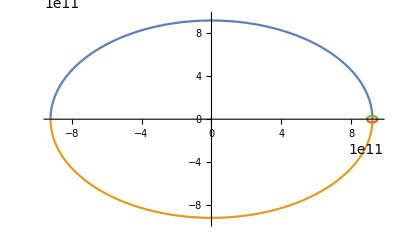

```mathematica
f[x_]=1.04405 r1(1-x^2/(1.045^2 r1^2))^(1/2)
g[x_,r_]=(r2^2-(x-r)^2)^(1/2)
Plot[{f[x],-f[x],g[x,(1+ecc)/2*r1],-g[x,(1+ecc)/2*r1]},{x,-ecc*r1,ecc*r1},PlotRange->{-ecc*r1,ecc*r1}]
```

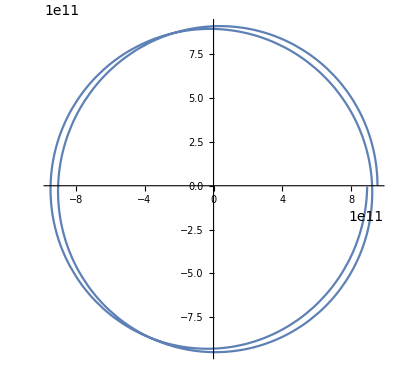

```mathematica
ParametricPlot[{1.045r1 Cos[t/monthLength]+r2 Cos[t],1.04405r1 Sin[t/monthLength]+r2 Sin[t]},{t,0,2*2π monthLength}]
```

```mathematica
fx[t_]=1.045r1 Cos[t/monthLength]+r2 Cos[t]
fy[t_]=1.04405r1 Sin[t/monthLength]+r2 Sin[t]
```

9.20749×10^11 Cos[0.441659 t]+3.015×10^10 Cos[t]

9.19912×10^11 Sin[0.441659 t]+3.015×10^10 Sin[t]

```mathematica
(L1/(4π σ r2^2))^(1/4)
```

162.515

```mathematica
R[t_]=Sqrt[(fx[t]+.045r1)^2+fy[t]^2]
r[t_]=((1.045r1 Cos[t/monthLength])^2+(1.04405r1 Sin[t/monthLength])^2)^(1/2)
```

√((3.96495×10^10+9.20749×10^11 Cos[0.441659 t]+3.015×10^10 Cos[t])^2+(9.19912×10^11 Sin[0.441659 t]+3.015×10^10 Sin[t])^2)

√(8.4778×10^23 Cos[0.441659 t]^2+8.46239×10^23 Sin[0.441659 t]^2)

```mathematica
temp[t_]=(L0/(4π σ R[t]^2))^(1/4)+(L1/(4π σ r2^2))^(1/4)
```

162.515+2.2062×10^8 (1/((3.96495×10^10+9.20749×10^11 Cos[0.441659 t]+3.015×10^10 Cos[t])^2+(9.19912×10^11 Sin[0.441659 t]+3.015×10^10 Sin[t])^2))^(1/4)

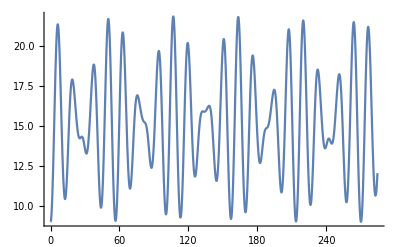

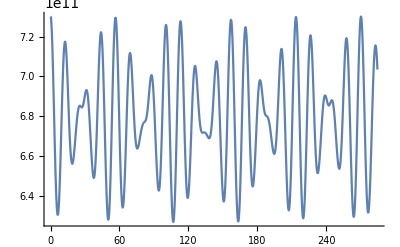

```mathematica
Plot[temp[t]*perc-274.15,{t,0,20*2π *monthLength}]
Plot[R[t]*perc-274.15,{t,0,20*2π monthLength}]
```

```mathematica
(*Comment from Jason to chekc git code merge*)
```